```mathematica
Quit[]
```

How mathematica works:  use “Shift -Enter “ to run the code, start with the running the Quit[] to clear previous calculations.
you can drop down the code and the plots with the button after the orange text, and see/ run the code and the plots

Default model of population of biofilm throughout the potato growing season:

```mathematica
(*Initial Parameters: Kill Switch, diffusion to plant, active bacterial diffusion to soil*)
f[a0p_,b0p_,d1p_,dp_,Ap_,tp_,sp_]:=Module[{a0=a0p,b0=b0p,d1=d1p,d=dp,Amin=Ap,tmin=tp,s=sp},
Kill=10;
Sp=1000;
Ss=5000;

T[t_]:=4.75+14.09*Sin[0.01057*t+0.3018]; (*Function for temperature in terms of time: curved fit from soil temperature data in the Netherlands*)
Aw[t_]:=0.97+0.0001*t; (*Linear relationship between water activity and time within the survivable water activity range for bacteria*)
Growth[t_]:=((T[t]-tmin)^2*(Aw[t]-Amin)); (*Ratkowksy square root equation for function of bacterial growth in terms of temperature, minimum temperature, water activity and minimum water activity*)
Growth2[t_]:=0.5*((T[t]-tmin)^2*(Aw[t]-Amin));
S[t_]:=G[t]*s*((G[t]+a0*B[t])/Sp)+G[t]*d; (*Patch transfer of GMO bacteria away from plant*)
P[t_]:=M[t]*d1; (*Patch transfer of GMO bacteria towards plant*)
P2[t_]:=A[t]*d1; (*Patch transfer of WT bacteria towards plant*)
S2[t_]:=B[t]*s*((B[t]+b0*G[t])/Sp)+B[t]*d; (*Patch transfer of GMO bacteria away from plant*)

(*ODEs to solve for GMO population towards plant and towards soil and WT population towards plant and towards soil*)
GMOp=G'[t]==Growth[t]*G[t]*((Sp-G[t]-a0*B[t])/Sp)+P[t]-S[t];
GMOs=M'[t]==(Growth2[t]-Kill)*M[t]*((Ss-M[t]-a0*A[t])/Ss)+S[t]-P[t];Wildp=B'[t]==Growth[t]*B[t]*((Sp-B[t]-b0*G[t])/Sp)+P2[t]-S2[t];Wilds=A'[t]==Growth2[t]*A[t]*((Ss-A[t]-b0*M[t])/Ss)+S2[t]-P2[t];

all={GMOp,GMOs,Wildp,Wilds};
 (*starting populations of the GMO and WT bacteria*)
init1={G[0]==500,M[0]==500,B[0]==500,A[0]==5000};
tmax=200;
Solution=NDSolveValue[{all,init1},{G[t],M[t],B[t],A[t]},{t,0,tmax}];
Solution]
sol=f[.5,.5,.1,.01,.95,10,0.01];
Plot[sol,{t,0,200},PlotStyle->{Purple,Blue,Green,Yellow},PlotLabels->{"GMO-plant", "GMO-soil", "WT-plant", "WT-soil"}, PlotRange->Full,PlotLabel->"bacterial popualtions over time",Frame->{True,True,False,False},FrameLabel->{"Time (days)","Population" }]
```

-Graphics-

Model with a 2 % temperature decrease:

```mathematica
g[a0p_,b0p_,d1p_,dp_,Ap_,tp_,sp_]:=Module[{a0=a0p,b0=b0p,d1=d1p,d=dp,Amin=Ap,tmin=tp,s=sp},
Kill=10;
Sp=1000;
Ss=5000;

T2[t_]:=0.98* (4.75+14.09*Sin[0.01057*t+0.3018]);
Aw[t_]:=0.97+0.0001*t;
Growth3[t_]:=((T2[t]-tmin)^2*(Aw[t]-Amin));
Growth4[t_]:=0.5*((T2[t]-tmin)^2*(Aw[t]-Amin));
S[t_]:=G[t]*s*((G[t]+a0*B[t])/Sp)+G[t]*d;
P[t_]:=M[t]*d1;
P2[t_]:=A[t]*d1;
S2[t_]:=B[t]*s*((B[t]+b0*G[t])/Sp)+B[t]*d;

GMOp1=G'[t]==Growth3[t]*G[t]*((Sp-G[t]-a0*B[t])/Sp)+P[t]-S[t];
GMOs1=M'[t]==(Growth4[t]-Kill)*M[t]*((Ss-M[t]-a0*A[t])/Ss)+S[t]-P[t];Wildp1=B'[t]==Growth3[t]*B[t]*((Sp-B[t]-b0*G[t])/Sp)+P2[t]-S2[t];Wilds1=A'[t]==Growth4[t]*A[t]*((Ss-A[t]-b0*M[t])/Ss)+S2[t]-P2[t];

all1={GMOp1,GMOs1,Wildp1,Wilds1};
init2={G[0]==500,M[0]==500,B[0]==500,A[0]==5000};
tmax=200;
Solution1=NDSolveValue[{all1,init2},{G[t],M[t],B[t],A[t]},{t,0,tmax}];
Solution1]
solu=g[.5,.5,.05,.01,.95,10,0.001];
Plot[solu,{t,0,200},PlotStyle->{Purple,Blue,Green,Yellow},PlotLabels->{"GMO-plant", "GMO-soil", "WT-plant", "WT-soil"}, PlotRange->Full,PlotLabel->"bacterial popualtions over time",Frame->{True,True,False,False},FrameLabel->{"Time (days)","Population" }]
```

-Graphics-

Model with a  2 % water activity decrease:

```mathematica
h[a0p_,b0p_,d1p_,dp_,Ap_,tp_,sp_]:=Module[{a0=a0p,b0=b0p,d1=d1p,d=dp,Amin=Ap,tmin=tp,s=sp},
Kill=10;
Sp=1000;
Ss=5000;

T[t_]:= (4.75+14.09*Sin[0.01057*t+0.3018]);
Aw2[t_]:=0.98*(0.97+0.0001*t);
Growth5[t_]:=((T[t]-tmin)^2*(Aw2[t]-Amin));
Growth6[t_]:=0.5*((T[t]-tmin)^2*(Aw2[t]-Amin));
S[t_]:=G[t]*s*((G[t]+a0*B[t])/Sp)+G[t]*d;
P[t_]:=M[t]*d1;
P2[t_]:=A[t]*d1;
S2[t_]:=B[t]*s*((B[t]+b0*G[t])/Sp)+B[t]*d;

GMOp2=G'[t]==Growth5[t]*G[t]*((Sp-G[t]-a0*B[t])/Sp)+P[t]-S[t];
GMOs2=M'[t]==(Growth6[t]-Kill)*M[t]*((Ss-M[t]-a0*A[t])/Ss)+S[t]-P[t];Wildp2=B'[t]==Growth5[t]*B[t]*((Sp-B[t]-b0*G[t])/Sp)+P2[t]-S2[t];Wilds2=A'[t]==Growth6[t]*A[t]*((Ss-A[t]-b0*M[t])/Ss)+S2[t]-P2[t];

all2={GMOp2,GMOs2,Wildp2,Wilds2};
init2={G[0]==500,M[0]==500,B[0]==500,A[0]==5000};
tmax=200;
Solution2=NDSolveValue[{all2,init2},{G[t],M[t],B[t],A[t]},{t,0,tmax}];
Solution2]
solu2=h[.4,.2,.05,.01,.95,7,0.001];
Plot[solu2,{t,0,200},PlotStyle->{Purple,Blue,Green,Yellow},PlotLabels->{"GMO-plant", "GMO-soil", "WT-plant", "WT-soil"}, PlotRange->Full,PlotLabel->"bacterial popualtions over time",Frame->{True,True,False,False},FrameLabel->{"Time (days)","Population" }]
```

-Graphics-

Order of parameters: Alpha, beta, D2, D1, Awmin, Tmin, S, Temperature, WaterActivity
2% decrease of each parameter at a time:

```mathematica
(*alpha*)
sol1=f[.5,.5,.05,.01,.95,10,0.001];
sol2=f[0.49,.5,.05,.01,.95,10,0.001];

(*beta*)
sol3=f[.5,.5,.05,.01,.95,10,0.001];
sol4=f[.5,0.49,.05,.01,.95,10,0.001];

(*D2*)
sol5=f[.5,.5,.05,.01,.95,10,0.001];
sol6=f[.5,.5,0.049,.01,.95,10,0.001];

(*D1*)
sol7=f[.5,.5,.05,.01,.95,10,0.001];
sol8=f[.5,.5,.05,0.0098,.95,10,0.001];

(*Awmin*)
sol9=f[.5,.5,.05,.01,.95,10,0.001];
sol10=f[.5,.5,.05,.01,0.931,10,0.001];

(*Tmin*)
sol11=f[.5,.5,.05,.01,.95,10,0.001];
sol12=f[.5,.5,.05,.01,.95,9.8,0.001];

(*s*)
sol13=f[.5,.5,.05,.01,.95,10,0.001];
sol14=f[.5,.5,.05,.01,.95,10,0.00984];

(*T*) sol15=g[.5,.5,.05,.01,.95,10,0.001];
(*Aw*) sol16=h[.5,.5,.05,.01,.95,10,0.001];
```

#### Calculation of the sensitivity plots, and plotting them:

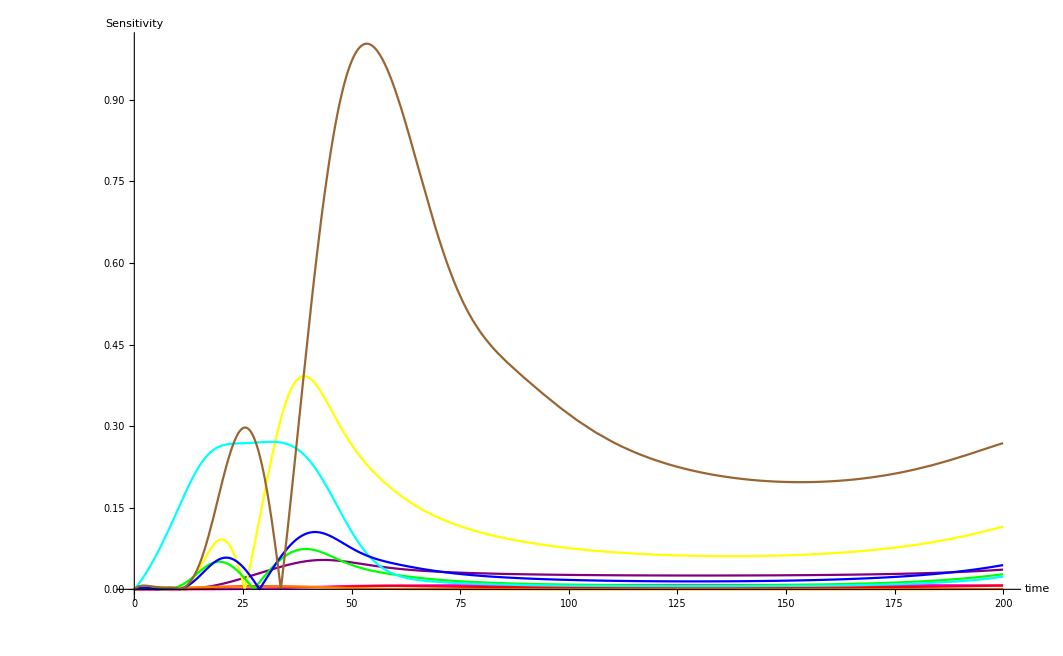

-Graphics-

-Graphics-

-Graphics-

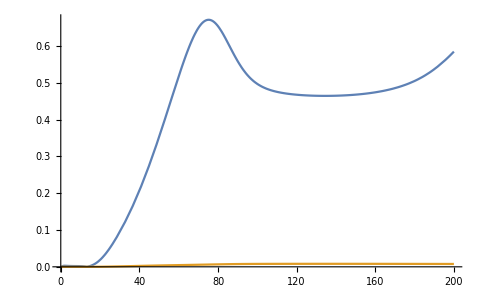

```mathematica
Alpha =Abs[Log[sol1[[1]]/sol2[[1]]]/Log[2]];
Betah=Abs[Log[sol3[[1]]/sol4[[1]]]/Log[2]];
D2=Abs[Log[sol5[[1]]/sol6[[1]]]/Log[2]];
D1=Abs[Log[sol7[[1]]/sol8[[1]]]/Log[2]];
Awmin=Abs[Log[sol9[[1]]/sol10[[1]]]/Log[2]];
Tmin=Abs[Log[sol11[[1]]/sol12[[1]]]/Log[2]];
Sss=Abs[Log[sol13[[1]]/sol14[[1]]]/Log[2]];
Temp= Abs[Log[sol7[[1]]/sol15[[1]]]/Log[2]];
Water = Abs[Log[sol7[[1]]/sol16[[1]]]/Log[2]];
Plot[{Alpha,Betah,D2,D1,Awmin,Tmin,Sss,Temp,Water},{t,0,200},AxesLabel->{"time", "Sensitivity"},PlotStyle->{Purple, Magenta, Red,Orange,Yellow, Green,Cyan, Blue, Brown},PlotRange->Full]


Plot[{Alpha,Betah},{t,0,200},Frame->{True,True,False,False},FrameLabel->{Style["Time (Days)",FontSize->18],Style["Sensitivity coefficient",FontSize->18]},PlotLabel->Style["Sensitivity over time for competition",FontSize->20],FrameTicksStyle->Directive[FontSize->16],PlotStyle->{Red,Blue},PlotLabels->{Style["Alpha            ",FontSize->13],Style["Beta               ",FontSize->13]},PlotRange->Full]

Plot[{Sss,D1,D2},{t,0,200},Frame->{True,True,False,False},FrameLabel->{Style["Time (Days)",FontSize->18],Style["Sensitivity coefficient",FontSize->18]},PlotLabel->Style["Sensitivity over time for diffusion",FontSize->20],FrameTicksStyle->Directive[FontSize->16],PlotStyle->{Blue,Purple,Magenta},PlotLabels->{Style["s                     .",FontSize->13],Style["D1                        .",FontSize->13], Style["D2                      .",FontSize->13]},PlotRange->Full]

Plot[{Awmin,Tmin},{t,0,200},Frame->{True,True,False,False},FrameLabel->{Style["Time (Days)",FontSize->18],Style["Sensitivity coefficient",FontSize->18]},PlotLabel->Style["Sensitivity over time for minimum temperature and water activity",FontSize->20],FrameTicksStyle->Directive[FontSize->16],PlotStyle->{Cyan,Red},PlotLabels->{Style["AW_min                  ",FontSize->13],Style["T_min                   ",FontSize->13]},PlotRange->Full]
```

#### Calculation of the sensitivity after 150 days:

```mathematica
(*alpha*)
sol1=f[.5,.5,.05,.01,.95,10,0.001]/.t->150
sol2=f[0.49,.5,.05,.01,.95,10,0.001]/.t->150

(*beta*)
sol3=f[.5,.5,.05,.01,.95,10,0.001]/.t->150
sol4=f[.5,0.49,.05,.01,.95,10,0.001]/.t->150

(*D2*)
sol5=f[.5,.5,.05,.01,.95,10,0.001]/.t->150
sol6=f[.5,.5,0.049,.01,.95,10,0.001]/.t->150

(*D1*)
sol7=f[.5,.5,.05,.01,.95,10,0.001]/.t->150
sol8=f[.5,.5,.05,0.0098,.95,10,0.001]/.t->150

(*Awmin*)
sol9=f[.5,.5,.05,.01,.95,10,0.001]/.t->150
sol10=f[.5,.5,.05,.01,0.931,10,0.001]/.t->150

(*Tmin*)
sol11=f[.5,.5,.05,.01,.95,10,0.001]/.t->150
sol12=f[.5,.5,.05,.01,.95,9.8,0.001]/.t->150

(*s*)
sol13=f[.5,.5,.05,.01,.95,10,0.001]/.t->150
sol14=f[.5,.5,.05,.01,.95,10,0.00984]/.t->150

(*T*) sol15=g[.5,.5,.05,.01,.95,10,0.001]/.t->150
(*Aw*) sol16=h[.5,.5,.05,.01,.95,10,0.001]/.t->150
```

{581.37,1.37533,828.682,4793.49}

{591.879,1.3751,824.114,4793.45}

{581.37,1.37533,828.682,4793.49}

{578.146,1.36772,835.125,4793.57}

{581.37,1.37533,828.682,4793.49}

{582.686,1.37985,826.036,4797.73}

{581.37,1.37533,828.682,4793.49}

{581.432,1.35043,828.726,4793.36}

{581.37,1.37533,828.682,4793.49}

{607.085,1.56697,780.18,4865.15}

{581.37,1.37533,828.682,4793.49}

{584.611,1.39454,822.558,4803.05}

{581.37,1.37533,828.682,4793.49}

{578.873,2.46527,826.232,4800.16}

{574.983,1.34006,840.723,4774.24}

{507.037,1.06429,965.985,4533.81}

```mathematica
Alpha =Abs[Log[sol1[[1]]/sol2[[1]]]/Log[2]]
Betah=Abs[Log[sol3[[1]]/sol4[[1]]]/Log[2]]
D2=Abs[Log[sol5[[1]]/sol6[[1]]]/Log[2]]
D1=Abs[Log[sol7[[1]]/sol8[[1]]]/Log[2]]
Awmin=Abs[Log[sol9[[1]]/sol10[[1]]]/Log[2]]
Tmin=Abs[Log[sol11[[1]]/sol12[[1]]]/Log[2]]
Sss=Abs[Log[sol13[[1]]/sol14[[1]]]/Log[2]]
Temp= Abs[Log[sol7[[1]]/sol15[[1]]]/Log[2]]
Water = Abs[Log[sol7[[1]]/sol16[[1]]]/Log[2]]
```

0.0258469

0.00802186

0.003262

0.000155151

0.0624419

0.00802015

0.00620881

0.0159362

0.197364